## CellVertexCoordinates-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 14:27:26
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

```mathematica
w=TemplateRandomSquareGrid[36, {-5,-5}, {5, 5}];
```

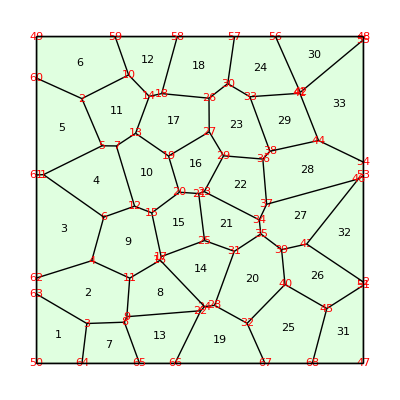

```mathematica
ShowTissue[w, "CellNumbers"-> True, "VertexNumbers"-> Red]
```

Determine the vertex numbers for cell 15

```mathematica
cvxc=CellVertexCoordinates[w,15]
```

{{-1.47561,-0.392682},{-0.631101,0.237572},{-0.0400254,0.197398},{0.138384,-1.24012},{-1.18936,-1.73276}}

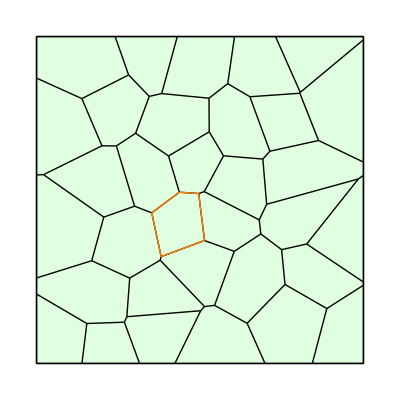

```mathematica
Show[ShowTissue[w], Boundary[cvxc, {Thick, Orange}]]
```

Determine the edge numbers for cell 15

```mathematica
c15=TissueCells[w][[15]]
```

{29,28,32,39,37}

Find the list of all edges

```mathematica
e=TissueEdges[w];
```

```mathematica
v=TissueVertices[w];
```

```mathematica
CellVertexCoordinates[c15, e, v]
```

{{-1.47561,-0.392682},{-0.631101,0.237572},{-0.0400254,0.197398},{0.138384,-1.24012},{-1.18936,-1.73276}}

```mathematica
CellVertexCoordinates[w]
```

{{{-5,-5},{-3.61061,-5.},{-3.46194,-3.77792},{-5.,-2.87641}},{{-5.,-2.38549},{-5.,-2.87641},{-3.46194,-3.77792},{-2.31278,-3.73779},{-2.23825,-3.56983},{-2.14998,-2.3895},{-3.31179,-1.85706}},{{-5.,0.76678},{-5.,-2.38549},{-3.31179,-1.85706},{-2.94306,-0.523013},{-4.78635,0.775441}},{{-4.78635,0.775441},{-2.94306,-0.523013},{-2.00098,-0.189368},{-2.55768,1.65368},{-2.99926,1.65762}},{{-5.,3.72852},{-5.,0.76678},{-4.78635,0.775441},{-2.99926,1.65762},{-3.61288,3.10124}},{{-5,5},{-5.,3.72852},{-3.61288,3.10124},{-2.1834,3.82476},{-2.5966,5.}},{{-3.61061,-5.},{-1.84951,-5.},{-2.31278,-3.73779},{-3.46194,-3.77792}},{{-2.23825,-3.56983},{-2.14998,-2.3895},{-1.21732,-1.84156},{0.138259,-3.25991},{0.0216111,-3.38759}},{{-3.31179,-1.85706},{-2.94306,-0.523013},{-2.00098,-0.189368},{-1.47561,-0.392682},{-1.18936,-1.73276},{-1.21732,-1.84156},{-2.14998,-2.3895}},{{-2.55768,1.65368},{-2.00098,-0.189368},{-1.47561,-0.392682},{-0.631101,0.237572},{-0.962273,1.346},{-1.96973,2.04081}},{{-3.61288,3.10124},{-2.99926,1.65762},{-2.55768,1.65368},{-1.96973,2.04081},{-1.55207,3.16979},{-2.1834,3.82476}},{{-0.69448,5.},{-2.5966,5.},{-2.1834,3.82476},{-1.55207,3.16979},{-1.17267,3.25495}},{{-1.84951,-5.},{-0.768323,-5.},{0.0216111,-3.38759},{-2.23825,-3.56983},{-2.31278,-3.73779}},{{-1.21732,-1.84156},{-1.18936,-1.73276},{0.138384,-1.24012},{1.04897,-1.56993},{0.445825,-3.22284},{0.138259,-3.25991}},{{-1.47561,-0.392682},{-0.631101,0.237572},{-0.0400254,0.197398},{0.138384,-1.24012},{-1.18936,-1.73276}},{{-0.962273,1.346},{-0.631101,0.237572},{-0.0400254,0.197398},{0.130299,0.256018},{0.719592,1.35183},{0.282196,2.08609}},{{-1.96973,2.04081},{-1.55207,3.16979},{-1.17267,3.25495},{0.274794,3.11388},{0.282196,2.08609},{-0.962273,1.346}},{{1.05585,5.},{-0.69448,5.},{-1.17267,3.25495},{0.274794,3.11388},{0.848255,3.55878}},{{-0.768323,-5.},{1.98882,-5.},{1.44128,-3.77111},{0.445825,-3.22284},{0.138259,-3.25991},{0.0216111,-3.38759}},{{0.445825,-3.22284},{1.04897,-1.56993},{1.86059,-1.03829},{2.4962,-1.51869},{2.60044,-2.58361},{1.44128,-3.77111}},{{-0.0400254,0.197398},{0.138384,-1.24012},{1.04897,-1.56993},{1.86059,-1.03829},{1.81272,-0.608213},{0.130299,0.256018}},{{0.130299,0.256018},{1.81272,-0.608213},{2.03846,-0.130601},{1.92215,1.25215},{0.719592,1.35183}},{{0.274794,3.11388},{0.282196,2.08609},{0.719592,1.35183},{1.92215,1.25215},{2.13752,1.49181},{1.52577,3.15848},{0.848255,3.55878}},{{2.30953,5.},{1.05585,5.},{0.848255,3.55878},{1.52577,3.15848},{3.05486,3.26477},{3.06726,3.2926}},{{1.98882,-5.},{3.43519,-5.},{3.87895,-3.32002},{2.60044,-2.58361},{1.44128,-3.77111}},{{5.,-2.60671},{5.,-2.50974},{3.26287,-1.34605},{2.4962,-1.51869},{2.60044,-2.58361},{3.87895,-3.32002}},{{1.81272,-0.608213},{2.03846,-0.130601},{4.84354,0.643048},{3.26287,-1.34605},{2.4962,-1.51869},{1.86059,-1.03829}},{{5.,0.753312},{5.,1.15909},{3.62583,1.81993},{2.13752,1.49181},{1.92215,1.25215},{2.03846,-0.130601},{4.84354,0.643048}},{{1.52577,3.15848},{2.13752,1.49181},{3.62583,1.81993},{3.05486,3.26477}},{{5,5},{2.30953,5.},{3.06726,3.2926},{5.,4.90254}},{{3.87895,-3.32002},{5.,-2.60671},{5,-5},{3.43519,-5.}},{{5.,-2.50974},{5.,0.753312},{4.84354,0.643048},{3.26287,-1.34605}},{{5.,1.15909},{5.,4.90254},{3.06726,3.2926},{3.05486,3.26477},{3.62583,1.81993}}}